```mathematica
simplifiedTable2=
Table[{Mean[First/@rs],Mean[Second/@rs]},
{rs,tableTotalppibar//inGroupsOf[2]}];
simplifiedTable4=
Table[{Mean[First/@rs],Mean[Second/@rs]},
{rs,tableTotalppibar//inGroupsOf[4]}];
simplifiedTable6=
Table[{Mean[First/@rs],Mean[Second/@rs]},
{rs,tableTotalppibar//inGroupsOf[6]}];
simplifiedTable10=
Table[{Mean[First/@rs],Mean[Second/@rs]},
{rs,tableTotalppibar//inGroupsOf[10]}];
```

```mathematica
simplifiedTable10//Length
```

48

```mathematica
evenSpacedTable=Table[{x,Interpolation[simplifiedTable10,x,InterpolationOrder->1]},{x,1.15,3.89,(3.89-1.15)/120}];
```

```mathematica
tableTotalppibar={pLabInv[m0@pi,m0@N938,#[[1]]],#[[2]]}&/@
{{0.09875,8.8700},{0.16000,13.600},{0.16520,15.800},{0.17600,17.700},{0.18101,21.000},{0.18900,21.200},{0.18980,23.120},{0.19100,22.200},{0.20400,28.000},{0.20600,29.300},{0.20930,31.000},{0.21220,33.740},{0.21870,38.440},{0.21885,33.400},{0.22000,38.600},{0.22200,39.300},{0.22740,44.480},{0.23063,42.700},{0.23413,46.900},{0.23600,47.700},{0.23645,52.000},{0.23800,50.300},{0.24330,55.350},{0.24684,48.100},{0.25100,58.200},{0.25300,59.100},{0.25371,55.300},{0.25599,60.000},{0.26021,56.400},{0.26168,62.900},{0.26460,67.900},{0.26600,66.200},{0.26800,68.100},{0.27040,70.260},{0.27071,67.500},{0.27520,63.000},{0.27536,67.200},{0.27600,71.000},{0.27632,62.700},{0.27920,70.740},{0.28100,71.900},{0.28285,67.200},{0.28300,72.200},{0.28303,66.000},{0.28637,65.900},{0.29033,67.700},{0.29100,70.600},{0.29260,69.760},{0.29303,63.500},{0.29552,67.800},{0.29600,68.800},{0.29800,68.800},{0.30242,64.000},{0.30297,64.600},{0.30407,63.100},{0.30600,65.500},{0.30760,63.800},{0.31100,62.300},{0.31293,59.300},{0.31300,62.700},{0.31811,58.700},{0.31930,59.430},{0.31941,57.200},{0.32050,64.000},{0.32330,55.600},{0.32594,55.500},{0.32700,55.000},{0.32800,56.400},{0.32812,54.500},{0.32848,52.200},{0.33138,52.100},{0.33367,50.200},{0.33571,50.500},{0.33728,48.200},{0.33788,52.900},{0.34074,49.000},{0.34100,48.800},{0.34220,58.000},{0.34300,48.800},{0.34436,44.500},{0.34500,47.060},{0.34797,44.900},{0.34867,46.100},{0.34985,48.300},{0.35144,42.700},{0.35298,43.500},{0.35491,43.100},{0.35600,42.900},{0.35800,41.500},{0.35853,41.000},{0.36201,39.300},{0.36549,39.800},{0.36911,38.800},{0.36950,38.460},{0.37100,38.100},{0.37227,38.200},{0.37274,36.800},{0.37300,38.300},{0.37812,35.600},{0.38176,36.500},{0.38351,33.400},{0.38600,33.300},{0.38890,31.100},{0.39430,32.400},{0.39971,31.600},{0.40100,31.100},{0.40512,30.500},{0.40626,33.000},{0.40640,29.970},{0.41055,29.300},{0.41500,30.830},{0.41600,29.000},{0.41612,28.900},{0.42156,28.100},{0.42407,30.200},{0.42716,28.700},{0.42736,27.890},{0.43000,27.800},{0.43262,27.000},{0.43500,28.190},{0.43809,26.200},{0.44311,26.800},{0.44312,26.400},{0.44500,27.000},{0.44935,26.000},{0.45500,26.730},{0.45881,25.980},{0.46000,26.600},{0.46065,24.900},{0.46925,26.730},{0.47400,26.360},{0.47500,26.180},{0.47723,25.200},{0.47968,25.980},{0.48900,26.400},{0.49008,27.000},{0.49320,26.700},{0.49500,26.500},{0.49900,27.040},{0.49903,28.900},{0.50047,27.230},{0.51085,26.500},{0.51300,27.490},{0.51500,26.700},{0.53155,27.570},{0.53500,27.190},{0.53625,34.000},{0.54188,28.400},{0.54452,29.500},{0.54705,28.060},{0.54808,29.440},{0.54911,27.000},{0.55000,28.520},{0.55500,27.880},{0.56251,27.150},{0.56500,29.360},{0.57281,27.000},{0.57500,28.810},{0.57600,29.550},{0.57630,32.600},{0.57796,29.110},{0.58310,29.310},{0.58765,30.000},{0.59132,29.960},{0.59338,31.100},{0.59500,30.960},{0.60878,29.910},{0.61400,30.190},{0.61742,34.600},{0.62200,32.800},{0.62416,30.710},{0.63200,32.140},{0.63686,35.900},{0.63892,34.900},{0.63952,33.340},{0.64259,34.980},{0.65000,34.020},{0.65100,36.650},{0.65486,34.840},{0.65820,40.000},{0.66400,39.590},{0.66800,37.560},{0.67019,37.790},{0.67300,40.690},{0.67530,37.460},{0.68200,43.560},{0.68300,46.000},{0.68487,43.600},{0.68551,39.740},{0.68700,41.590},{0.68891,44.600},{0.69000,41.880},{0.69265,44.820},{0.69300,45.180},{0.69367,42.300},{0.69571,42.990},{0.69911,49.000},{0.70081,42.970},{0.70200,45.680},{0.70500,44.580},{0.71100,46.310},{0.71326,45.800},{0.71500,44.700},{0.71610,45.550},{0.71711,45.070},{0.71800,46.000},{0.71832,49.600},{0.72300,45.460},{0.72650,45.500},{0.73035,44.700},{0.73100,45.900},{0.73646,45.430},{0.73866,45.100},{0.73981,50.000},{0.74000,44.140},{0.74100,44.590},{0.74257,45.290},{0.74300,44.100},{0.75681,44.100},{0.75914,48.300},{0.76000,41.600},{0.76500,41.620},{0.76611,44.400},{0.77002,44.470},{0.77400,40.380},{0.77500,41.540},{0.77714,39.600},{0.77800,38.630},{0.77944,45.300},{0.78847,39.200},{0.79000,38.220},{0.79100,36.630},{0.79237,39.160},{0.79971,42.100},{0.80400,36.670},{0.80760,37.060},{0.81200,36.480},{0.81500,35.730},{0.81800,36.170},{0.81996,39.000},{0.82400,35.800},{0.83300,35.120},{0.84000,35.630},{0.84326,35.100},{0.84500,36.100},{0.84715,34.900},{0.85100,36.090},{0.85952,37.100},{0.86500,36.660},{0.86949,36.700},{0.87000,38.640},{0.87300,38.450},{0.87363,37.600},{0.87754,37.430},{0.88300,40.230},{0.89000,39.940},{0.89387,37.400},{0.89779,37.380},{0.90100,41.600},{0.90386,39.000},{0.90700,44.410},{0.91500,44.210},{0.91810,39.000},{0.92020,43.900},{0.92611,40.200},{0.93100,49.580},{0.93900,51.580},{0.94000,50.290},{0.94041,48.500},{0.94429,47.900},{0.94532,46.370},{0.94835,48.200},{0.95455,50.000},{0.96147,55.200},{0.96500,55.560},{0.96553,48.130},{0.96555,54.600},{0.96958,55.130},{0.97100,57.780},{0.98070,60.100},{0.98574,53.320},{0.98800,59.880},{0.99000,58.540},{0.99376,58.600},{0.99584,54.200},{0.99600,60.090},{0.99681,56.000},{0.99786,59.220},{1.00094,61.200},{1.00200,60.580},{1.01500,58.090},{1.01600,59.750},{1.01603,56.760},{1.01610,57.800},{1.02007,58.460},{1.02114,60.500},{1.02700,57.800},{1.04000,55.180},{1.04019,59.300},{1.04420,54.500},{1.04529,55.170},{1.04832,55.020},{1.05000,53.800},{1.06045,54.400},{1.06500,50.220},{1.06940,50.400},{1.07354,50.670},{1.07500,49.750},{1.07555,48.820},{1.08158,51.800},{1.08900,46.690},{1.09000,45.630},{1.09572,45.700},{1.09880,44.700},{1.10100,44.410},{1.10173,48.900},{1.10277,44.840},{1.11500,41.410},{1.11588,41.520},{1.12700,41.020},{1.14000,39.350},{1.14108,42.800},{1.14110,39.600},{1.14510,39.540},{1.15100,39.290},{1.16500,37.970},{1.16600,38.150},{1.17600,38.140},{1.18126,38.300},{1.19000,37.260},{1.19500,37.190},{1.19545,36.660},{1.20100,37.180},{1.20144,37.600},{1.20330,35.900},{1.20753,35.770},{1.21500,36.380},{1.22600,36.760},{1.24000,36.120},{1.24175,36.500},{1.25100,36.570},{1.26500,36.190},{1.27500,36.450},{1.27780,35.500},{1.28100,36.420},{1.28193,36.000},{1.28199,35.520},{1.29000,36.160},{1.29608,34.450},{1.31200,36.560},{1.31500,36.230},{1.32118,35.600},{1.33200,36.630},{1.34000,36.570},{1.34900,36.640},{1.35500,36.610},{1.36500,36.390},{1.38000,36.680},{1.38845,35.700},{1.39000,36.130},{1.39303,34.600},{1.39561,35.720},{1.39900,36.650},{1.40900,36.620},{1.41500,35.880},{1.42051,35.900},{1.43300,36.540},{1.44000,36.110},{1.45100,36.490},{1.46500,35.630},{1.47600,36.070},{1.49000,35.820},{1.49400,36.060},{1.49607,33.480},{1.50088,35.500},{1.51500,35.060},{1.52097,35.300},{1.53100,35.540},{1.54000,34.630},{1.54115,34.500},{1.56500,34.390},{1.57200,35.080},{1.58119,34.700},{1.59000,34.000},{1.59548,31.810},{1.60400,34.750},{1.62139,34.700},{1.62200,34.620},{1.67200,34.640},{1.68155,34.300},{1.71900,34.700},{1.75983,34.300},{1.77300,35.080},{1.78500,35.110},{1.82099,34.000},{1.82100,35.510},{1.85100,35.490},{1.86900,35.580},{1.87913,34.800},{1.91600,36.030},{1.92026,35.200},{1.95100,36.080},{1.96700,36.180},{2.00010,35.700},{2.01600,36.380},{2.05000,36.420},{2.06700,36.340},{2.10200,36.100},{2.11979,35.400},{2.16800,36.060},{2.21700,35.770},{2.26000,35.480},{2.26600,35.440},{2.36600,34.630},{2.41400,34.350},{2.47000,33.800},{2.52000,34.055},{2.52200,33.530},{2.56800,33.320},{2.61400,32.950},{2.62000,33.468},{2.66500,32.890},{2.72000,33.017},{2.75000,32.500},{2.82000,32.758},{2.92000,32.546},{3.02000,32.411},{3.10010,30.900},{3.12000,32.299},{3.15000,31.300},{3.22000,32.174},{3.32000,31.973},{3.40000,31.400},{3.42000,31.746},{3.52000,31.569},{3.62000,31.334},{3.72000,31.064},{3.82000,30.901},{3.90000,30.000},{3.93000,30.739},{4.03000,30.519},{4.10000,30.800},{4.13000,30.363},{4.23000,30.170},{4.33000,30.058},{4.43000,29.902},{4.50000,30.200},{4.53000,29.744},{4.63000,29.600},{4.63747,29.400},{4.73000,29.487},{4.83000,29.360},{4.90000,29.600},{4.93000,29.237},{4.95000,29.100},{5.03000,29.120},{5.13000,28.988},{5.23000,28.881},{5.33000,28.766},{5.44000,28.680},{5.54000,28.586},{5.64000,28.450},{5.74000,28.355},{5.75000,29.100},{5.84000,28.256},{5.94000,28.149},{6.00000,28.500},{6.04000,28.072},{6.24000,27.884},{6.44000,27.704},{6.64000,27.518},{6.65000,27.900},{6.84000,27.356},{6.94000,27.236},{7.00000,28.400},{7.19863,31.000},{8.00000,27.640},{8.05000,28.400},{9.20000,25.000},{10.00000,25.500}};
tableElasticppibar={pLabInv[m0@pi,m0@N938,#[[1]]],#[[2]]}&/@
{{0.09875,1.8470},{0.14956,2.9000},{0.21648,9.6000},{0.21885,11.300},{0.22828,12.800},{0.24684,17.000},{0.25599,20.100},{0.26733,21.400},{0.27071,22.500},{0.27520,21.200},{0.29303,22.500},{0.30297,26.400},{0.32050,28.700},{0.33138,19.500},{0.33571,16.000},{0.33788,17.400},{0.35052,15.100},{0.35190,20.800},{0.37800,12.290},{0.38261,12.400},{0.40400,10.100},{0.40626,13.800},{0.40800,10.410},{0.42188,11.400},{0.42700,9.0000},{0.44888,10.300},{0.45200,8.9000},{0.47100,9.2000},{0.49008,10.420},{0.50900,9.1500},{0.52300,9.8000},{0.52845,11.400},{0.53155,11.400},{0.54700,9.9900},{0.54911,13.000},{0.55600,10.240},{0.56500,10.800},{0.57281,12.190},{0.58200,16.200},{0.58600,11.340},{0.60900,12.860},{0.61390,13.710},{0.61698,13.900},{0.62500,12.190},{0.64054,14.800},{0.65700,13.920},{0.65793,16.200},{0.65800,15.320},{0.67530,16.980},{0.68300,18.900},{0.68700,17.070},{0.69061,18.860},{0.69900,19.070},{0.70692,19.950},{0.71399,20.500},{0.72628,19.870},{0.73100,18.900},{0.73257,16.600},{0.74257,19.400},{0.75000,19.910},{0.76189,18.940},{0.77500,17.560},{0.77714,17.190},{0.77827,16.100},{0.79800,14.910},{0.82586,15.750},{0.83803,14.900},{0.84800,13.200},{0.84954,14.100},{0.85400,14.470},{0.87466,14.400},{0.89417,25.100},{0.90386,14.800},{0.91903,14.100},{0.92400,18.800},{0.94349,21.800},{0.95500,21.620},{0.95947,18.000},{0.97900,23.160},{0.98977,26.600},{0.99500,26.420},{0.99988,22.200},{1.00290,26.580},{1.00400,24.220},{1.01704,27.300},{1.02400,26.300},{1.03016,18.600},{1.04200,26.010},{1.04220,24.600},{1.04529,26.700},{1.06700,23.650},{1.08000,25.100},{1.08059,19.100},{1.08800,19.480},{1.09068,20.000},{1.09111,14.600},{1.10600,17.950},{1.12091,19.820},{1.12339,17.700},{1.12500,18.290},{1.13099,22.000},{1.16400,13.660},{1.16500,15.010},{1.17400,15.730},{1.21400,12.450},{1.21659,14.100},{1.23000,14.600},{1.25000,13.310},{1.26000,13.800},{1.27900,12.800},{1.32300,13.090},{1.33630,12.000},{1.33900,12.627},{1.34100,12.730},{1.34200,12.380},{1.34300,13.507},{1.34500,12.714},{1.34700,12.987},{1.34900,13.401},{1.35100,13.384},{1.35300,12.394},{1.35500,12.763},{1.35700,12.724},{1.35900,12.851},{1.36100,12.507},{1.36300,12.430},{1.36500,12.367},{1.36700,12.395},{1.36900,13.332},{1.37100,12.491},{1.37300,13.035},{1.37500,12.852},{1.37700,12.040},{1.37900,12.673},{1.38000,15.000},{1.38100,12.488},{1.38200,12.530},{1.38300,12.286},{1.38500,12.670},{1.38700,12.662},{1.38900,13.354},{1.39100,13.054},{1.39300,12.626},{1.39500,12.126},{1.39700,12.651},{1.39900,12.956},{1.40100,12.606},{1.40300,12.361},{1.40500,12.340},{1.40700,12.091},{1.40900,12.130},{1.41100,11.937},{1.41300,12.712},{1.41500,12.478},{1.41700,12.510},{1.41900,12.521},{1.42100,12.321},{1.42300,12.271},{1.42500,12.594},{1.42700,12.536},{1.42900,12.260},{1.43100,12.407},{1.43300,12.346},{1.43500,12.532},{1.43700,12.407},{1.43900,12.266},{1.44100,12.167},{1.44300,12.266},{1.44500,11.950},{1.44700,11.776},{1.44900,11.907},{1.45100,12.042},{1.45300,11.786},{1.45500,11.568},{1.45700,11.246},{1.45900,11.767},{1.46100,12.017},{1.46300,11.754},{1.46500,11.413},{1.46700,11.436},{1.46900,11.206},{1.47000,10.870},{1.47100,10.828},{1.47300,11.052},{1.47500,11.119},{1.47700,11.575},{1.47900,11.645},{1.48100,11.434},{1.48300,12.639},{1.48500,11.643},{1.48700,11.702},{1.48900,11.210},{1.49100,11.502},{1.49300,11.313},{1.49500,11.368},{1.49700,11.523},{1.49900,11.163},{1.50300,11.690},{1.50310,10.000},{1.50900,10.390},{1.56700,10.210},{1.59000,9.6500},{1.60000,9.0000},{1.60300,9.8200},{1.71000,10.400},{1.85000,11.100},{2.00000,7.3400},{2.01000,7.9400},{2.10000,9.6900},{2.14000,9.3000},{2.26000,8.9100},{2.29000,8.5000},{2.70000,7.7000},{2.75000,7.2000},{2.77000,7.2000},{2.79990,7.8000},{3.00000,7.5700},{3.15000,6.1000},{3.25000,7.3000},{3.65000,6.9700},{3.92000,6.8400},{4.00000,6.6200},{4.13000,5.6000},{4.16000,5.7700},{4.50000,6.2100},{4.63747,3.5000},{4.75000,4.7000},{4.95000,6.1000},{5.00000,5.8500},{5.17000,5.6000},{6.00000,5.3000},{7.00000,5.1300},{8.00000,5.0700},{8.90020,4.8200},{9.99990,4.5900},{10.8000,4.7700},{11.2000,4.4300},{13.0000,4.7200},{15.0000,4.6200},{15.9000,4.2000},{16.0000,4.0800},{16.2000,4.3600},{17.0000,4.1100},{18.9000,4.3900},{25.2000,3.3500},{32.8200,3.2170},{35.3900,3.5500},{40.1000,3.3200},{42.0200,3.3590},{45.3400,3.5060},{48.6100,3.4560},{50.0000,3.4800},{50.9600,3.4140},{54.7400,3.2670},{55.1000,3.0450},{70.0000,3.3900},{100.000,3.2800},{140.000,3.3600},{147.000,3.2400},{175.000,3.3800},{200.000,3.3200},{205.000,3.1800},{360.000,3.6100}};
```

```mathematica
σTotalppibar[eCM_]:=Piecewise[{
{0.,eCM≤m0@pi+m0@N938},
{σRes[N938,1/2,pi,-1,eCM],eCM<1.78},
{Interpolation[simplifiedTable4,eCM,InterpolationOrder->1],eCM≤3.5}
},13.7*eCM^0.158+35.9eCM^-0.90
];
σResppibar[eCM_]:=If[eCM≤m0@pi+m0@N938,0.,σRes[N938,1/2,pi,-1,eCM]];
σFullElasticppibar[eCM_]:=Piecewise[{
{0.,eCM≤m0@pi+m0@N938},
{σResEl[N938,1/2,pi,-1,eCM],eCM<1.75},
{Interpolation[tableElasticppibar,eCM,InterpolationOrder->1],eCM≤2.0}
},fitHERA[pLab[m0@pi,m0@N938,eCM],1.76,11.2,-0.64,0.043,0.]
];
σResElasticppibar[eCM_]:=If[eCM≤m0@pi+m0@N938,0.,σResEl[N938,1/2,pi,-1,eCM]];
σElasticppibar[eCM_]:=If[eCM<1.96,0.,σFullElasticppibar[eCM]-σResElasticppibar[eCM]];
σStringppibar[eCM_]:=If[eCM<1.8,0.,σTotalppibar[eCM]-σElasticppibar[eCM]-σResppibar[eCM]];
```

```mathematica
ptsTableppibar=Table[{p,Interpolation[tableTotalppibar,pLabInv[m0@pi,m0@N938,p],InterpolationOrder->1]},{p,m0@pi+m0@N938,5.,0.01}];
```

```mathematica
ptsTotalppibar=Monitor[
Table[{eCM,σTotalppibar@eCM},{eCM,0.,5.,0.01}],
ProgressIndicator[eCM,{0.,5.}]
];
```

```mathematica
ptsResppibar=Monitor[
Table[{p,σResppibar@pLabInv[m0@pi,m0@N938,p]},{p,0.,5.,0.01}],
ProgressIndicator[p,{0.,5.}]
];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

$Aborted

```mathematica
ptsElasticppibar=Monitor[
Table[{p,σElasticppibar@pLabInv[m0@pi,m0@N938,p]},{p,1.,5.,0.01}],
ProgressIndicator[p,{1.,5.}]
];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
ptsStringppibar=Monitor[
Table[{p,σStringppibar@pLabInv[m0@pi,m0@N938,p]},{p,0.,5.,0.01}],
ProgressIndicator[p,{0.,5.}]
];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
ListLinePlot[{
ptsResppibar,
ptsElasticppibar,
ptsStringppibar,
ptsTotalppibar
},PlotRange->All,PlotLegends->{"Resonance","Elastic","String","Total"},AxesLabel->{"pLab","σ"}]
```

$Aborted

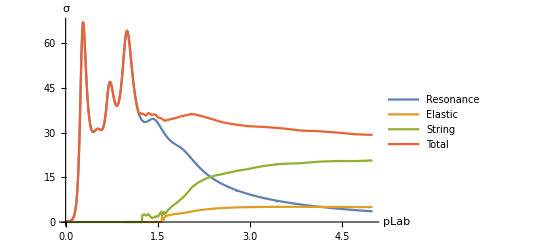

```mathematica
{pLabInv[m0@pi,m0@N938,#[[1]]],#[[2]]}&/@ptsElasticppibar
```

```mathematica
%//Rasterize
```

-Graphics-

```mathematica
ptsFullElasticppibar=Monitor[
Table[{p,fitHERA[p,1.76,11.2,-0.64,0.043,0.]},{p,1.,5.,0.01}],
ProgressIndicator[p,{0.,5.}]
];
```

```mathematica
ptsResElasticppibar=Monitor[
Table[{p,σResElasticppibar@pLabInv[m0@pi,m0@N938,p]},{p,0.,5.,0.01}],
ProgressIndicator[p,{0.,5.}]
];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
ptsNonresElasticppibar=Monitor[
Table[{p,σElasticppibar@pLabInv[m0@pi,m0@N938,p]},{p,0.,5.,0.01}],
ProgressIndicator[p,{0.,5.}]
];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

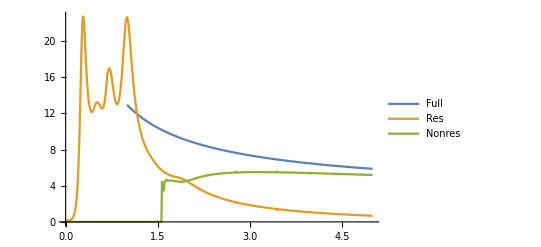

```mathematica
ListLinePlot[{ptsFullElasticppibar,ptsResElasticppibar,ptsNonresElasticppibar},PlotRange->All,PlotLegends->{"Full","Res","Nonres"}]
```

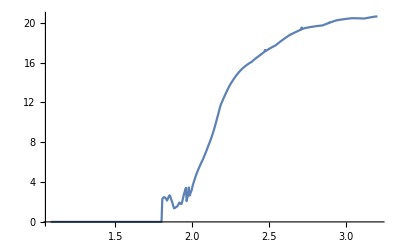

```mathematica
{pLabInv[m0@pi,m0@N938,#[[1]]],#[[2]]}&/@ptsStringppibar//ListLinePlot
```

```mathematica
ptsSimplified={pLabInv[m0@pi,m0@N938,#[[1]]],#[[2]]}&/@ptsElasticppibar;
```

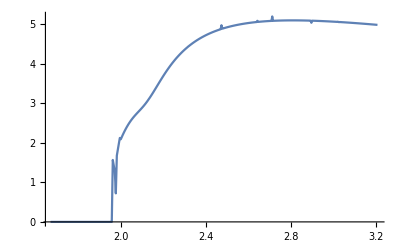

```mathematica
ptsSimplified//ListLinePlot
```

```mathematica
pts={{1.9731653453352889,0},{1.9778955090378092,0.7221708961331075},{1.9826146081217777,1.6775911789733637},{1.987322717362553,1.8282982137804389},{1.9920199107440208,1.9773037804234095},{1.996706261469033,2.1243553115606852},{2.001381841969709,2.0922678233127066},{2.00604672391761,2.1492764511353153},{2.0107009782337757,2.2040673473572667},{2.0153446750986337,2.256509753091077},{2.0199778839617735,2.3065125750878774},{2.024600673551593,2.354026533955409},{2.0292131118848107,2.3990457550502855},{2.033815266275851,2.4415948465710677},{2.0384072033460985,2.4817400210887692},{2.042988989033026,2.5195773594520325},{2.0475606885991944,2.5552354427783284},{2.0521223666411244,2.588873893977813},{2.056674087098047,2.6206808041238885},{2.0612159132605283,2.650852278838923},{2.065747907778969,2.6796379734212046},{2.0702701326719857,2.707161769039814},{2.0747826493346713,2.7340407397176474},{2.079285518546735,2.7601884358864908},{2.0837788004805247,2.7859912007838536},{2.088262554708935,2.8117126335129115},{2.092736840213198,2.8375979162754756},{2.09720171539056,2.86387395676483},{2.1016572380618506,2.890741748274725},{2.1061034654789323,2.9183704168824764},{2.110540454332052,2.9468930251699117},{2.114968260757073,2.976407648323322},{2.11938694034261,3.0069668927567665},{2.1237965481370518,3.0386171834106435},{2.128197138655485,3.07153813288431},{2.132588765886514,3.106298228903343},{2.136971483298978,3.1397407800150585},{2.1413453438485743,3.17529688365037},{2.1457103999843743,3.2116163038336953},{2.1500667036552534,3.248569178795476},{2.154414306316219,3.2860781794972036},{2.158753258934646,3.3239491406530863},{2.1630836119964205,3.36229429942255},{2.1674054155119937,3.400401600950202},{2.1717187190223424,3.4387256282845113},{2.176023571604847,3.476966994130522},{2.1803200218790755,3.515024222968462},{2.1846081180124886,3.5528052952583584},{2.1888879077260555,3.590227872910825},{2.193159438299789,3.6272194726117304},{2.1974227565781996,3.663716222852833},{2.2016779089756664,3.699654948295194},{2.2059249414817317,3.7350237829782014},{2.2101638996663144,3.769750397300567},{2.2143948286848514,3.8038166719019006},{2.2186177732833583,3.8371975973036054},{2.222832777803419,3.8698793293309617},{2.2270398861871006,3.9018513016078105},{2.231239141981798,3.9330995105784163},{2.2354305883450056,3.963623972582184},{2.2396142680490208,3.993424418196809},{2.2437902234855764,4.022508446281082},{2.2479584966704116,4.050867629360547},{2.2521191292477662,4.078523549913991},{2.256272162494822,4.105481246619466},{2.2604176373260687,4.132287593146266},{2.2645555942976117,4.157345543571433},{2.26868607361142,4.182177799319945},{2.272809115119507,4.206493556273912},{2.276924758328055,4.2302026622958655},{2.2810330424014795,4.253224270448237},{2.285134006166434,4.275688811785235},{2.2892276881157594,4.297489767589031},{2.2933141264123758,4.318899250053782},{2.297393358893116,4.339460678345782},{2.3014654230725125,4.359617172773566},{2.305530356146519,4.379243349328274},{2.309588194996189,4.398354503793663},{2.313638976191298,4.416964732539846},{2.317682735993914,4.436311355463621},{2.321719510361918,4.4527304096132205},{2.325749334952476,4.469927544271741},{2.3297722451254623,4.4866723888551885},{2.3337882759468336,4.502982225204532},{2.337797462191954,4.518870524193059},{2.34179983834888,4.534349372332844},{2.34579543862159,4.549430387855038},{2.3497842969331777,4.564124925540106},{2.353766446928999,4.57844407809731},{2.3577419219797697,4.5923930402801325},{2.3617107551846277,4.6059987133688765},{2.3656729793741476,4.619254072642612},{2.369628627113319,4.632137915526921},{2.3735777307044787,4.644742698198578},{2.377520322190204,4.657049467768202},{2.3814564333561696,4.669021104122562},{2.385386095733962,4.6806937178967765},{2.3893093406038566,4.692075477066865},{2.3932261989975565,4.703174382768356},{2.397136701700897,4.7140127885450065},{2.401040879256509,4.724554032955142},{2.4049387619664513,4.734849300414014},{2.4088303798948005,4.744891214376983},{2.4127157628702163,4.75468620017994},{2.4165949404884617,4.764240714870487},{2.4204679421148976,4.773561172703445},{2.424334796886939,4.782650195163734},{2.428195533716481,4.791524004643418},{2.432050181292292,4.80017803192284},{2.4358987680823763,4.80862122319891},{2.4397413223363005,4.8168467149466245},{2.443577872087498,4.824889511639493},{2.4474084451555354,4.832741090069465},{2.4512330691483504,4.8403904669826865},{2.4550517714644653,4.8478497432469165},{2.458864579295166,4.855141566713931},{2.4626715196266553,4.862249914745913},{2.4664726192421766,4.869185919469471},{2.4702679047241127,4.8759354132279356},{2.4740574024560553,4.977337879986869},{2.4778411386248456,4.889000883492676},{2.481619139222596,4.895287541280899},{2.4853914300486766,4.901422035188384},{2.4891580367116823,4.907406921257145},{2.4929189846313746,4.913246394347572},{2.4966742990405937,4.918941912596903},{2.500424004987152,4.924501298564096},{2.504168127335701,4.929923447349053},{2.507906690769573,4.935212891215859},{2.511639719792603,4.9403726073217715},{2.5153672387309247,4.945405497465239},{2.519089271734746,4.95031400011934},{2.5228058427800986,4.955102355585735},{2.5265169756705714,4.959769182921138},{2.530222694039017,4.9643225362266215},{2.5339230213492403,4.9687625283973},{2.5376179808976627,4.973091593658731},{2.5413075958149705,4.97731238668047},{2.5449918890677377,4.981426911945554},{2.5486708834600322,4.985440049973114},{2.5523446016350007,4.989348922656417},{2.556013066076436,4.993158922207325},{2.559676299110321,4.996871425204506},{2.563334322906359,5.000491282003922},{2.566987159479482,5.00401411987562},{2.5706348306913394,5.007446717255904},{2.5742773582517735,5.010789891191596},{2.5779147637202735,5.014034025910009},{2.5815470685074113,5.0172111332629985},{2.585174293876262,5.020297019866934},{2.5887964609438066,5.023305008810414},{2.592413590682319,5.0262257646032005},{2.5960257039207333,5.029069758344629},{2.5996328213459985,5.031837478551125},{2.603234963504413,5.034528208132364},{2.606832150802949,5.037144668109787},{2.610424403510553,5.03968828388782},{2.61401174175944,5.0421605247283985},{2.617594185546365,5.044562723784882},{2.621171754733884,5.04689558173448},{2.6247444690515986,5.049162022126747},{2.6283123480973845,5.05136249509019},{2.6318754113386085,5.053498135099394},{2.635433678113331,5.055570723886115},{2.638987167631491,5.057495764377873},{2.642535898976082,5.088333683003839},{2.6460798911043097,5.061417213987895},{2.649619162848742,5.06324795594271},{2.6531537329184385,5.064612040454049},{2.6566836199000736,5.066975199607612},{2.6602088422590437,5.068153961946781},{2.6637294183405613,5.070214566120822},{2.6672453663707367,5.071526418410148},{2.6707567044576495,5.072979504345271},{2.6742634505924054,5.0745343783046515},{2.677765622650182,5.075915192512287},{2.6812632383912636,5.077265516360654},{2.6847563154620606,5.078567195367281},{2.6882448713961247,5.079810820398458},{2.6917289236151434,5.08103434284603},{2.695208489429932,5.082188341132287},{2.698683586041409,5.083304374249797},{2.702154230541561,5.084430494002591},{2.7056204399143997,5.085405329030415},{2.7090822310369074,5.086390998490882},{2.7125396206799675,5.198627578032289},{2.715992625509293,5.088237622385982},{2.7194412620863373,5.089099860585967},{2.7228855468691973,5.089922405016314},{2.7263254962135104,5.090705930023123},{2.7297611263733335,5.091451141748225},{2.733192453502022,5.092153490599048},{2.7366194936530914,5.092830744713575},{2.7400422627810728,5.093463740645125},{2.7434607767423604,5.094263743303153},{2.7468750512960454,5.094625750336669},{2.7502851021047467,5.0951548056312825},{2.7536909447354274,5.09565006998269},{2.7570925946602065,5.096113301010496},{2.7604900672571584,5.096542808957521},{2.763883377811105,5.096938477141253},{2.7672725415144024,5.0973052974288775},{2.770657573467715,5.0976386368692035},{2.774038488680782,5.097942703887396},{2.777415302073179,5.098216803927712},{2.780788028475066,5.098461446869182},{2.7841566826279345,5.0986771119562615},{2.78752127918534,5.098864291586089},{2.7908818327136298,5.099023498065537},{2.7942383576926653,5.0991541981589465},{2.7975908685165325,5.099259357568625},{2.800939379494246,5.099337687143938},{2.804283904850449,5.09938967606598},{2.807624458726103,5.099415822327458},{2.810961055179169,5.099416768320882},{2.814293708185287,5.099392720868443},{2.8176224316384415,5.09934427074813},{2.8209472393516255,5.099271774365578},{2.8242681450574953,5.099175620298656},{2.8275851624090205,5.099056230644418},{2.8308983049801224,5.098913952029445},{2.8342075862663134,5.098873485265262},{2.837513019685323,5.098561771339092},{2.840814618577721,5.098353424418454},{2.8441123962075334,5.0981228994225045},{2.8474063657628537,5.097870866723489},{2.8506965403564433,5.097598933202592},{2.8539829330263324,5.097306672070433},{2.8572655567364085,5.096994405811929},{2.8605444243770046,5.096662287176211},{2.863819548765477,5.096313306379554},{2.8670909426467786,5.095942829691718},{2.8703586186940306,5.095553566883719},{2.873622589509079,5.095145861814231},{2.8768828676230567,5.094718824350744},{2.880139465496932,5.0942748770621815},{2.883392395522054,5.093813458132015},{2.886641670020696,5.09333471206682},{2.889887301246586,5.092838698467306},{2.89312930138544,5.090567646267415},{2.8963676825554865,5.038498738092034},{2.8996024568079815,5.091252350797637},{2.902833636127728,5.090692031969166},{2.9060612324335833,5.090114938647263},{2.9092852575789627,5.089522297771902},{2.9125057233523375,5.088914515102375},{2.915722641477734,5.08829183721191},{2.918936023615218,5.0876075381157175},{2.9221458813613834,5.087002519843711},{2.9253522262498306,5.086336326559689},{2.9285550697516425,5.085656061440619},{2.9317544232758563,5.08496194876069},{2.934950298169928,5.0842542394789785},{2.9381427057201983,5.083533124812119},{2.941331657152345,5.082798791007175},{2.9445171636318404,5.08205147894899},{2.947699236264398,5.081291395778918},{2.9508778860964195,5.080518714307766},{2.9540531241154326,5.079733688538499},{2.9572249612505286,5.0789364358783535},{2.960393408372794,5.078127191838246},{2.96355847629574,5.077306138271921},{2.9667201757757233,5.076473457785507},{2.969878517512371,5.075629338372719},{2.9730335121489926,5.074773954265826},{2.9761851702729927,5.073907478222427},{2.979333502416282,5.073030000381397},{2.9824785190556793,5.072141954142771},{2.985620230613315,5.071243238410148},{2.9887586474570234,5.070334141387895},{2.991893779900741,5.0694147874848134},{2.995025638204894,5.06848533806345},{2.9981542325767845,5.067545996294662},{3.0012795731709745,5.0665968579031},{3.004401670089662,5.065638098547995},{3.007520533383061,5.064669875260723},{3.01063617304977,5.063692330547999},{3.013748599037141,5.062705612340761},{3.016857821241648,5.061709864439273},{3.019963849509246,5.065430546918451},{3.02306669363573,5.059691844897935},{3.026166363367093,5.055016217077931},{3.0292628683998766,5.05763938251787},{3.0323562183815183,5.056600553970187},{3.0354464229107023,5.0555531795614765},{3.038533491537697,5.054497972045949},{3.0416174337646997,5.053078466105485},{3.0446982590461684,5.052364409286731},{3.0477759767891603,5.0513485212944635},{3.0508505963536603,5.050199688471204},{3.0539221270529073,5.0491060470981495},{3.0569905781537225,5.048005061134173},{3.0600559588768297,5.046896835674565},{3.063118278397173,5.045781500176617},{3.066177545844236,5.044659163137805},{3.0692337703023536,5.043529192937275},{3.0722869608110233,5.042393758553539},{3.0753371263652123,5.041246030673562},{3.0783842759156648,5.040096167984716},{3.0814284183692027,5.0389498345492605},{3.084469562589028,5.037784271433003},{3.0875077173950167,5.036615945363355},{3.0905428915640174,5.035441455251095},{3.093575093830141,5.03426094690688},{3.0966043328850508,5.033074399096624},{3.099630617378251,5.031882064910022},{3.102653955917371,5.030682156451009},{3.1056743570684455,5.0294856969334925},{3.1086918293561983,5.028272575447041},{3.111706381264316,5.027056030329413},{3.114718021235725,5.02583578396101},{3.1177267576728656,5.024610227498675},{3.1207325989379564,5.023379337898926},{3.123735553353272,5.022143532393755},{3.1267356292013986,5.020902567873776},{3.129732834725505,5.019656072970717},{3.1327271781296004,5.018405807517453},{3.1357186675787942,5.017150182231241},{3.1387073111995534,5.01588921348733},{3.141693117079957,5.014624839133585},{3.1446760932699465,5.013355278924494},{3.14765624778158,5.01208122887238},{3.150633588589279,5.010802765913185},{3.153608123630073,5.009519964492493},{3.1565798608038467,5.008232677235379},{3.1595488079735796,5.006941642012198},{3.162514972965587,5.0056462642284325},{3.1654783635697594,5.004346838518153},{3.168438987539797,5.003043434333147},{3.171396852593444,5.001736120657943},{3.174351966412722,5.00042496585262},{3.1773043366441587,4.99911003706096},{3.1802539708990185,4.997791400695966},{3.1832008767535274,4.996469125229807},{3.186145061749099,4.995143266379625},{3.189086533392555,4.993813898166483},{3.192025299156349,4.992481077521126},{3.194961366478785,4.991144868388339},{3.1978947427642326,4.989805331811583},{3.200825435383347,4.98846252833418},{3.203753451673278,4.987116517686099},{3.206678798937887,4.985767358476839}};
```

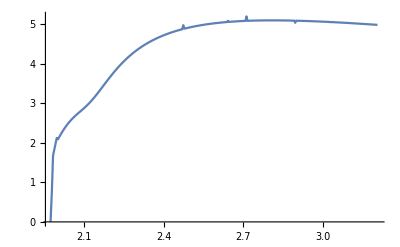

```mathematica
ListLinePlot[pts]
```

```mathematica
{{1.8,0.},{1.975,0.}}~Join~Table[{Mean[First/@rs],Mean[Second/@rs]},
{rs,pts//inGroupsOf[3]}]
```

{{1.8,0.},{1.975,0.},{1.97789,0.799921},{1.99202,1.97665},{2.00604,2.14854},{2.01997,2.30568},{2.03381,2.44079},{2.04756,2.55456},{2.06121,2.65039},{2.07478,2.7338},{2.08826,2.81177},{2.10165,2.891},{2.11497,2.97676},{2.12819,3.07215},{2.14134,3.17555},{2.15441,3.2862},{2.1674,3.40047},{2.18032,3.51493},{2.19316,3.62705},{2.20592,3.73481},{2.21862,3.83696},{2.23124,3.93286},{2.24379,4.02227},{2.25627,4.10543},{2.26868,4.18201},{2.28103,4.25304},{2.29331,4.31862},{2.30553,4.37907},{2.31768,4.43534},{2.32977,4.48653},{2.3418,4.53422},{2.35376,4.57832},{2.36567,4.61913},{2.37752,4.65694},{2.38931,4.69198},{2.40104,4.72447},{2.41271,4.75461},{2.42433,4.78258},{2.4359,4.80855},{2.44741,4.83267},{2.45886,4.85508},{2.47027,4.90749},{2.48162,4.89524},{2.49292,4.9132},{2.50417,4.92988},{2.51537,4.94536},{2.52652,4.95973},{2.53762,4.97306},{2.54867,4.98541},{2.55967,4.99684},{2.57063,5.00742},{2.58155,5.01718},{2.59241,5.0262},{2.60323,5.0345},{2.61401,5.04214},{2.62474,5.04914},{2.63543,5.05552},{2.64608,5.071},{2.65668,5.06658},{2.66724,5.07157},{2.67776,5.07591},{2.68824,5.0798},{2.69868,5.08331},{2.70908,5.12347},{2.71944,5.08909},{2.72976,5.09144},{2.74004,5.09352},{2.75028,5.09514},{2.76049,5.09653},{2.77066,5.09763},{2.78079,5.09845},{2.79088,5.09901},{2.80094,5.09933},{2.81096,5.09941},{2.82095,5.09926},{2.8309,5.09895},{2.84081,5.09835},{2.8507,5.09759},{2.86054,5.09666},{2.87036,5.09555},{2.88014,5.09427},{2.88989,5.09225},{2.8996,5.07348},{2.90928,5.08952},{2.91893,5.08763},{2.92855,5.08565},{2.93814,5.08353},{2.9477,5.08129},{2.95722,5.07893},{2.96672,5.07647},{2.97618,5.0739},{2.98562,5.07124},{2.99502,5.06848},{3.0044,5.06563},{3.01375,5.0627},{3.02307,5.06005},{3.03236,5.0566},{3.04162,5.05331},{3.05085,5.05022},{3.06005,5.04689},{3.06923,5.04353},{3.07838,5.0401},{3.08751,5.03661},{3.0966,5.03307},{3.10567,5.02948},{3.11472,5.02583},{3.12373,5.02214},{3.13273,5.0184},{3.14169,5.01462},{3.15063,5.0108},{3.15955,5.00694},{3.16844,5.00304},{3.1773,4.99911},{3.18614,4.99514},{3.19496,4.99114},{3.20375,4.98712}}

```mathematica
pts={{2.01298,4.08957},{2.05891,5.93332},{2.10384,7.60645},{2.14785,9.62448},{2.19099,11.8857},{2.2333,13.3665},{2.27484,14.4379},{2.31563,15.2175},{2.35573,15.7593},{2.39516,16.1886},{2.43395,16.6593},{2.47214,17.1056},{2.50975,17.4548},{2.54681,17.7907},{2.58334,18.2172},{2.61936,18.6103},{2.6549,18.9261},{2.68997,19.1831},{2.72459,19.4272},{2.75877,19.5375},{2.79254,19.6255},{2.82591,19.6942},{2.85889,19.7995},{2.89149,19.9928},{2.92374,20.1639},{2.95563,20.2851},{2.98718,20.3579},{3.0184,20.4203},{3.0493,20.4568},{3.07989,20.4481},{3.11019,20.4328},{3.14019,20.4847},{3.16991,20.5672},{3.19642,20.6261}};
```

```mathematica
evenSpacedTable={{1.90,0.}}~Join~Table[{x,Interpolation[pts,x,InterpolationOrder->1]},{x,1.926,3.2,(3.2-1.926)/50}]
```

InterpolatingFunction::dmval: Input value {1.926} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.95148} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.97696} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{{1.9,0.},{1.926,0.597966},{1.95148,1.6208},{1.97696,2.64363},{2.00244,3.66647},{2.02792,4.6893},{2.0534,5.71213},{2.07888,6.67697},{2.10436,7.63029},{2.12984,8.79865},{2.15532,10.016},{2.1808,11.3516},{2.20628,12.4208},{2.23176,13.3126},{2.25724,13.984},{2.28272,14.5885},{2.3082,15.0755},{2.33368,15.4614},{2.35916,15.7966},{2.38464,16.0741},{2.41012,16.3701},{2.4356,16.6786},{2.46108,16.9763},{2.48656,17.2395},{2.51204,17.4756},{2.53752,17.7065},{2.563,17.9797},{2.58848,18.2733},{2.61396,18.5514},{2.63944,18.7887},{2.66492,18.9995},{2.6904,19.1861},{2.71588,19.3658},{2.74136,19.4813},{2.76684,19.5585},{2.79232,19.6249},{2.8178,19.6775},{2.84328,19.7497},{2.86876,19.858},{2.89424,20.0074},{2.91972,20.1426},{2.9452,20.2455},{2.97068,20.3198},{2.99616,20.3758},{3.02164,20.4241},{3.04712,20.4542},{3.0726,20.4502},{3.09808,20.4389},{3.12356,20.4559},{3.14904,20.5093},{3.17452,20.5774},{3.2,20.6341}}

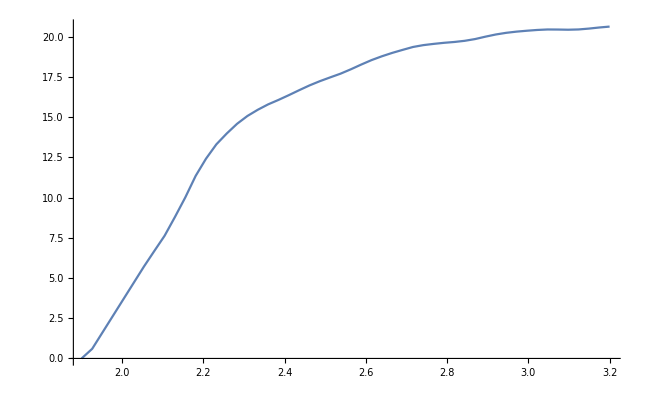

```mathematica
%//ListLinePlot
```

```mathematica
Second/@evenSpacedTable
```

{0.,0.597966,1.6208,2.64363,3.66647,4.6893,5.71213,6.67697,7.63029,8.79865,10.016,11.3516,12.4208,13.3126,13.984,14.5885,15.0755,15.4614,15.7966,16.0741,16.3701,16.6786,16.9763,17.2395,17.4756,17.7065,17.9797,18.2733,18.5514,18.7887,18.9995,19.1861,19.3658,19.4813,19.5585,19.6249,19.6775,19.7497,19.858,20.0074,20.1426,20.2455,20.3198,20.3758,20.4241,20.4542,20.4502,20.4389,20.4559,20.5093,20.5774,20.6341}